```mathematica
worlddata=Import["https://covid.ourworldindata.org/data/owid-covid-data.csv"];
```

```mathematica
(*names={"Japan","Taiwan","Australia","United States","United Kingdom","India","France","Germany","Italy","New Zealand","Brazil","South Korea","Sweden","Thailand","China"};*)
(*names={"Japan","Taiwan","Australia","United States","United Kingdom","India","Italy","New Zealand","South Korea","Sweden","China"};*)
(*names={"Japan","Taiwan","Malaysia","Thailand","Vietnam","India","Indonesia","Mongolia","Singapore","Philippines","South Korea","China"};
namesLabel={"日本","台湾","マレーシア","タイ","ベトナム","インド","インドネシア","モンゴル","シンガポール","フィリピン","韓国","中国"}.08;
namesLabel=names;*)
names={"Japan","United Kingdom","United States","France","Germany","Italy","Sweden","South Korea","Thailand","India","Indonesia","Canada","New Zealand","Taiwan"}
```

{Japan,United Kingdom,United States,France,Germany,Italy,Sweden,South Korea,Thailand,India,Indonesia,Canada,New Zealand,Taiwan}

```mathematica
startdate={2020,5,1};
enddate={2021,10,10};
startdateObj=DateObject[startdate];
date=4;
newDeathsSmoothed=10;
newDeathsSmoothedPerMillion=16;
newCasesSmoothedPerMillion=13;
newCasesSmoothed=7;
peopleVaccinatedPerHundred=42;
peopleFullyVaccinatedPerHundred=43;
newCases=6;
font="Helvetica Neue";
fontsize=12;
```

```mathematica
names={"Japan"};
Do[
country=names[[k]];
Which[
country=="New Zealand",
drate0=0.018;delay0=20;drate1=0.018;delay1=20;,
country=="Taiwan",
drate0=0.05;delay0=12;drate1=0.045;delay1=20;,
country=="Japan",
drate0=0.018;delay0=20;drate1=0.007;delay1=30;,
country=="United Kingdom",
drate0=0.024;delay0=17;drate1=0.004;delay1=30;,
country=="United States",
drate0=0.016;delay0=17;drate1=0.016;delay1=24;,
country=="France",
drate0=0.014;delay0=14;drate1=0.009;delay1=24;,
country=="Germany",
drate0=0.035;delay0=20;drate1=0.012;delay1=24;,
country=="Italy",
drate0=0.024;delay0=17;drate1=0.015;delay1=24;,
country=="Sweden",
drate0=0.018;delay0=17;drate1=0.003;delay1=24;,
country=="South Korea",
drate0=0.023;delay0=17;drate1=0.004;delay1=30;,
country=="Thailand",
drate0=0.012;delay0=14;drate1=0.012;delay1=8;,
country=="India",
drate0=0.008;delay0=7;drate1=0.011;delay1=12;,
country=="Indonesia",
drate0=0.024;delay0=3;drate1=0.04;delay1=14;,
country=="Canada",
drate0=0.02;delay0=14;drate1=0.006;delay1=14;
];
dataTmp=Cases[worlddata,x_?(#1[[3]]==country&)][[All,{date,newDeathsSmoothedPerMillion,newCasesSmoothedPerMillion,peopleFullyVaccinatedPerHundred}]];
data=DeleteCases[dataTmp,x_?(DateObject[#1[[1]]]<startdateObj&)];
dmin=0.02;
dmax=50;
vac[x_]:={x[[1]], Exp[Log[dmax] x[[2]]/100 + Log[dmin](1-x[[2]]/100)]};
fig1=Show[
DateListLogPlot[data[[All,{1,2}]],
PlotStyle->{{Gray,Thickness[0.002]}},
Joined->False,
PlotMarkers->"⊙",
PlotLegends->Style[country,Black,20],
GridLines->{None,Flatten[Table[{1,2,3,4,5,6,7,8,9}10^m,{m,-3,3}]]},
GridLinesStyle->{{Thickness[0.001]},{Thickness[0.001]}},
(*GridLines->{{{2020,7,1},{2020,10,1},{2021,1,1},{2021,4,1},{2021,7,1},{2021,10,1}},{160}}*)
(*DateTicksFormat->{"MonthShort"},*)
FrameStyle->Directive[fontsize,Black,FontFamily->font],Frame->True,
FrameTicksStyle->{{Black,Orange},Black},
FrameTicks->{{Automatic,{{dmin,"0%"},{Exp[(Log[dmin]+Log[dmax])/2],"50%"},{dmax,"100%"}}},Automatic},
PlotRange->{{{2020,10,1},enddate},{dmin,dmax}}],
DateListLogPlot[ d=delay0;
Table[{DatePlus[DateObject[data[[i,1]]],d],drate0 data[[i,3]]} ,{i,1,Length[data]}],
(*DatePlus[DateObject[startdate],d]*),FrameTicks->{{Automatic,None},Automatic},
PlotLegends->{Style[ToString[drate0]<>"×("<>ToString[delay0]<>"日前の感染者数)",Red]},
PlotRange->All,
PlotStyle->{{Red}}],
DateListLogPlot[ d=delay1;
Table[{DatePlus[DateObject[data[[i,1]]],d],drate1 data[[i,3]]} ,{i,1,Length[data]}],(*DatePlus[DateObject[startdate],d]*),FrameTicks->{{Automatic,None},Automatic},
PlotLegends->{Style[ToString[drate1]<>"×("<>ToString[delay1]<>"日前の感染者数)",Blue]},
PlotRange->All,
PlotStyle->{{Blue}}],
DateListLogPlot[vac/@data[[All,{1,4}]],
PlotStyle->{{Orange,Thickness[0.01],Opacity[0.5]}},
Joined->True,Filling->Axis,
GridLines->{None,Flatten[Table[{1,2,3,4,5,6,7,8,9}10^m,{m,-3,3}]]},
GridLinesStyle->{{Thickness[0.001]},{Thickness[0.001]}}]];
Export["~/"<>country<>".pdf",fig1],{k,1,Length[names]}];
```

```mathematica
nhkdata=Drop[Import["https://www3.nhk.or.jp/n-data/opendata/coronavirus/nhk_news_covid19_domestic_daily_data.csv"],1];
nhkdatasmooth=Table[{nhkdata[[i,1]],Mean[Table[nhkdata[[i-j,4]],{j,0,6}]],nhkdata[[i,4]]},{i,7,Length[nhkdata]}];
nhkdatasmoothcase=Table[{nhkdata[[i,1]],Mean[Table[nhkdata[[i-j,2]],{j,0,6}]],nhkdata[[i,2]]},{i,7,Length[nhkdata]}];
```

Import::nfurl: Unable to retreive data from https://www3.nhk.or.jp/n-data/opendata/coronavirus/nhk_news_covid19_domestic_daily_data.csv. Consult Internal`$LastInternalFailure for potential information.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,1].

0.018

0.007

{-∞,-∞}

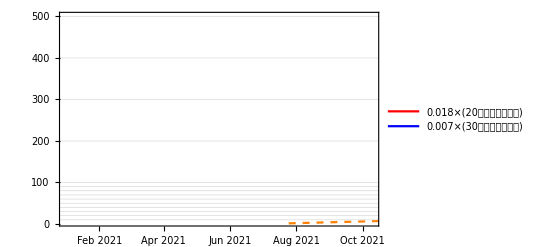

~/tmp.pdf

```mathematica
kmax=1;
drate0=0.018
drate1=0.007
{Max[drate1 nhkdatasmoothcase[[All,2]]],Max[drate0 nhkdatasmoothcase[[All,2]]]}
fig1=Show[
DateListLogPlot[nhkdatasmooth[[All,{1,2}]],
PlotStyle->{{Gray,Thickness[0.002]}},
Joined->False,
PlotMarkers->"⊙",
PlotLegends->Style["日本・死者数.08",Gray],
GridLines->{None,Flatten[Table[{1,2,3,4,5,6,7,8,9}10^m,{m,1,3}]]},
GridLinesStyle->{{Thickness[0.001]},{Thickness[0.001]}}
(*GridLines->{{{2020,7,1},{2020,10,1},{2021,1,1},{2021,4,1},{2021,7,1},{2021,10,1}},{160}}*),
(*DateTicksFormat->{"MonthShort"},*)
FrameStyle->Directive[fontsize,Black,FontFamily->font],Frame->True,
FrameTicks->{{Automatic,None},Automatic},
PlotRange->{{{2021,1,1},enddate},{5,500}}],
(*DateListLogPlot[
nhkdatasmooth[[All,{1,3}]],PlotStyle->{{Black,Thin}},PlotMarkers->"⊙",Joined->False],*)
(*DateListLogPlot[nhkdatasmooth[[All,{1,2}]],PlotStyle->Purple,PlotMarkers->"×"],*)
DateListLogPlot[ d=20;
Table[{DatePlus[DateObject[nhkdatasmoothcase[[i,1]]],d],drate0 nhkdatasmoothcase[[i,2]]} ,{i,1,Length[nhkdatasmoothcase]}],
(*DatePlus[DateObject[startdate],d]*),FrameTicks->{{Automatic,None},Automatic},
PlotLegends->{Style[ToString[drate0]<>"×(20日前の感染者数)",Red]},
PlotRange->All,
PlotStyle->{{Red}}],
DateListLogPlot[ d=30;
Table[{DatePlus[DateObject[nhkdatasmoothcase[[i,1]]],d],drate1 nhkdatasmoothcase[[i,2]]} ,{i,1,Length[nhkdatasmoothcase]}],(*DatePlus[DateObject[startdate],d]*),FrameTicks->{{Automatic,None},Automatic},
PlotLegends->{Style[ToString[drate1]<>"×(30日前の感染者数)",Blue]},
PlotRange->All,
PlotStyle->{{Blue}}],
DateListLogPlot[Table[
{DatePlus[DateObject[{2021,8,4}],i],9 (1.4)^(i/5)},{i,-10,100}],
Joined->True,
PlotStyle->{{Orange,Dashed,Thick}},
PlotLegends->Style["R=1.4, 世代時間=5日.08",Orange]
]]
Export["~/tmp.pdf",fig1]
```